```mathematica
SatisfiabilityInstances
```

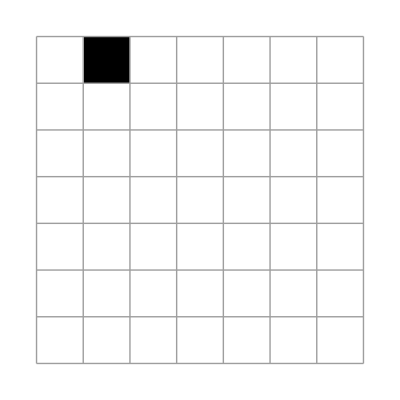

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/fiver2.m"];
looker2=plt[({{xNW11, xN11, xN12, xN13, xN14, xN15, xNE13}, {xW11, x11, x12, x13, x14, x15, xE15}, {xW21, x21, x22, x23, x24, x25, xE25}, {xW31, x31, x32, x33, x34, x35, xE35}, {xW41, x41, x42, x43, x44, x45, xE45}, {xW51, x51, x52, x53, x54, x55, xE55}, {xSW51, xS51, xS52, xS53, xS54, xS55, xSE55}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

```mathematica
Implies
```

```mathematica
⇒
```

```mathematica
cnf[x⇒False]
```

CNF | DNF
¬x | ¬x

```mathematica
life44
```

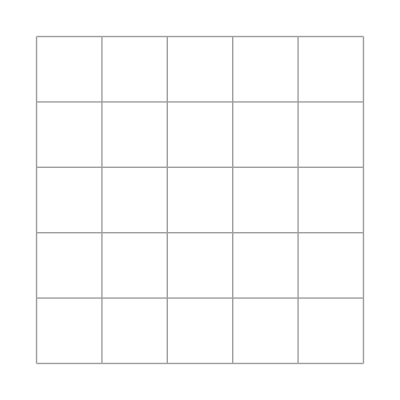
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
X0=({{x11, x12, x13, x14, x15}, {x21, x22, x23, x24, x25}, {x31, x32, x33, x34, x35}, {x41, x42, x43, x44, x45}, {x51, x52, x53, x54, x55}})/.endGame[[1]];
plt/@NestList[updateLife2[{5,5}][ #]&,
X0,3]
```